#### Interpolación por Polinomios de Lagrange

Para empezar, importamos todos los datos que vamos a utilizar en este Notebook, incluindo los splines para la próxima sección

```mathematica
SetDirectory[NotebookDirectory[]];
data1=Import["data21.txt","Table"];
data2=Import["data22.txt","Table"];
interppol1=Import["poly21.txt","Table"];
interppol2=Import["poly22.txt","Table"];
interpspline1=Import["spline21.txt","Table"];
interpspline2=Import["spline22.txt","Table"];
```

Y aquí ponemos todos los datos que van en algún momento en algún gráfico:

```mathematica
Points1= ListPlot[data1,PlotStyle->PointSize[0.02]];
Points2= ListPlot[data2,PlotStyle->PointSize[0.02]];
InterpFortranLagrange1=ListPlot[interppol1,PlotStyle->{PointSize[0.01],Green}];
InterpFortranLagrange2=ListPlot[interppol2,PlotStyle->{PointSize[0.01],Red}];
InterpFortranSpline1=ListPlot[interpspline1,PlotStyle->{PointSize[0.01],Cyan}];
InterpFortranSpline2=ListPlot[interpspline2,PlotStyle->{PointSize[0.01],Orange}];
InterpMathSpline1=Plot[Interpolation[data1,{x},Method->"Spline"],{x,0,4},PlotStyle->Green];
InterpMathSpline2=Plot[Interpolation[data2,{x},Method->"Spline"],{x,0,4},PlotStyle->Red];
```

Ahora que tenemos todo lo que necesitamos para hacer gráficas,  podemos finalmente hacer la que se pide. Pintaremos la interpolación de más datos de roja, y la de menos en verde, como indicado arriba:

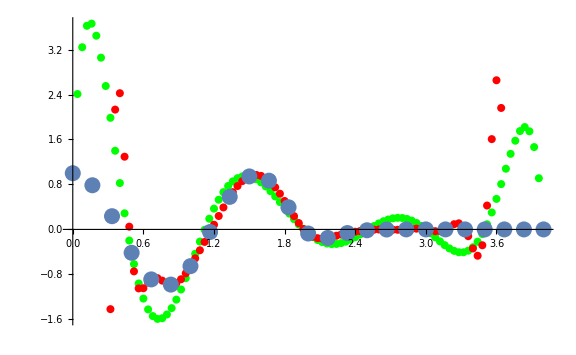

```mathematica
Show[InterpFortranLagrange1,InterpFortranLagrange2,Points2]
```

Aqui es importante hacer una aclaración: Cerca de 0 y de 4, la función roja parece menos densa o que directamente no está pintada. Esto no es verdad, es solo un artefacto de como Mathematica ha decido escojer los intervalos para que se puedan ver las tres funciones. Note que los datos están entre  , y la interpolación verde en . No obstante, la roja está aproximadamente en . Ingenuamente, podríamos asumir que eso significa que tenemos un problema en nuestro código o nuestra implementación de la interpolación polinimial, pero esto no es cierto: Ese es un ‘problema’ de interpolaciones polinimiales en general, en otros contextos llamadas de overfitting, que se resume al hecho de que son malas aproximaciones.

Porque las comillas en ‘problemas’? Porque es una interpolación perfecta, sin ningún problema: Perfectamente conecta los datos de manera suave (infinitamente diferenciable), entonces hace lo que debería hacer. Eso no signifca que eso es lo que nosotros queremos que haga: No preserva el comportamiento de cualquier que sea la función que generó los datos y no se aproxima a ella con más datos. 

 Para ilustrar ese punto, haré una pequeña divagación matemática. Suponga que tenemos una función  que no conocemos pero podemos medir. Como buenos matemáticos, decidimos hacer  muestras uniformes de la función en el intervalo , de manera que la evaluamos en los puntos  para  y tenemos los puntos  como datos de la interpolación. Sea   la interpolación polinomial con esos  datos. Como físicos, esperamos que , o sea, que cuanto más datos experimentales tengamos, mejor será nuestra aproximación y, con datos infinitos, tengamos una aproximación perfecta. Eso no es cierto. Para un ejemplo ilustrativo, si tomamos  en , la aproximación es perfecta para  , mala para  y arbitrariamente peor para  arbitrariamente grande.

## Interpolación por Splines Cúbicos

Para la primera parte, representamos los 3 gráficos que se piden:

```mathematica
Show[InterpFortranLagrange1,InterpFortranSpline1,Points1]
```

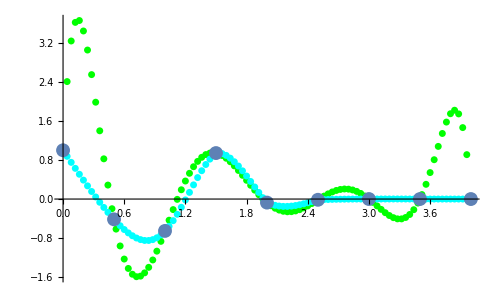

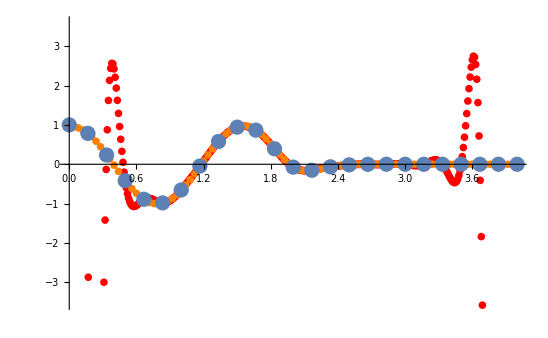

```mathematica
Show[InterpFortranLagrange2,InterpFortranSpline2,Points2]
```

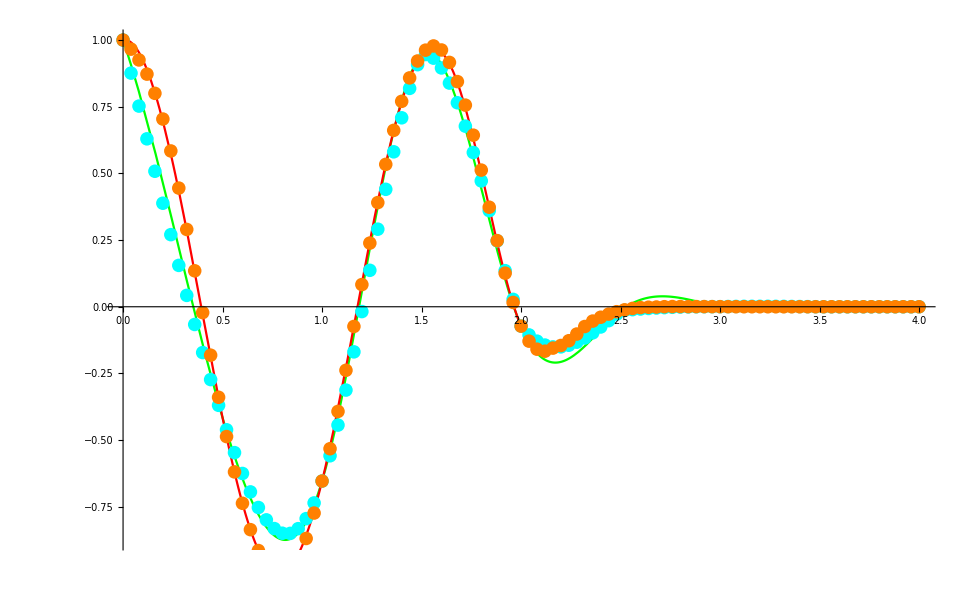

```mathematica
Show[InterpMathSpline1,InterpMathSpline2,InterpFortranSpline1,InterpFortranSpline2]
```

En el que podemos percibir que el spline de los n=8 de Fortran es ligeramente diferente del de Mathematica, especialmente en el intervalo . No podría decir exactamente el porque, pero mi intuición es que estará relacionado a las condiciones de borde que encojemos al principio, principalmente porque la diferencia basicamente no se nota para n=24, algo que debería pasar por la convergencia de los splines a la función original.